```mathematica
BoxGfx[point_]:=Graphics[Line[{point,point+{0,1},point+{1,1},point+{1,0},point}]];
BoxNetwork[n_]:=Module[{i,points,cp,adj,gfxlist,randparam,t},
t=AbsoluteTime[];
points=Table[{0,0},{i,1,n}];
cp={0,0};
randparam=Floor[n^(2/5)];
Print[AbsoluteTime[]-t];
For[i=2,i≤n,i++,
adj=RandomInteger[{-randparam,randparam}];
If[Mod[i,2]==0,
cp=cp+{0,adj};
,
cp=cp+{adj,0};
];
points[[i]]=cp;
];
Print[AbsoluteTime[]-t];
gfxlist=Table[BoxGfx[points[[i]]],{i,1,n}];
Print[AbsoluteTime[]-t];
Show[gfxlist]
];
```

0.00014

0.00035

0.000516

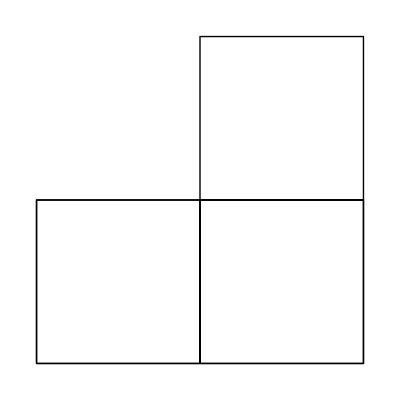

```mathematica
BoxNetwork[5]
```

0.000384

0.00157

0.00261

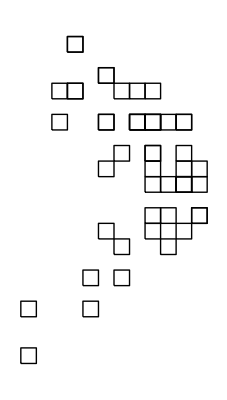

```mathematica
BoxNetwork[50]
```

0.00163

0.006625

0.01204

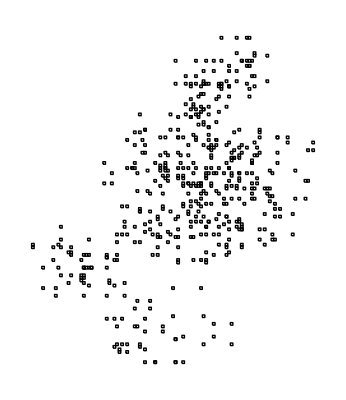

```mathematica
BoxNetwork[500]
```

0.00084

0.041041

0.082484

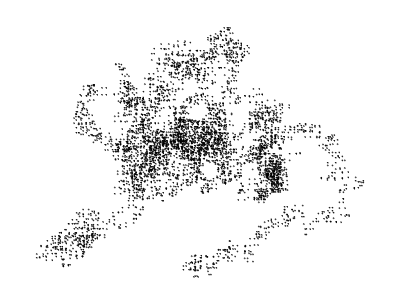

```mathematica
BoxNetwork[5000]
```

```mathematica
BoxNetwork[50000]
```

0.007538

0.361363

0.772816

-Graphics-